# MA2330

On Monday I jumbled something up from section 1.7 while explaining why Theorem 8 is true

The matrix V=(v_1 v_2… v_p) is n×p.  If p>n then V is a short and wide matrix.  
	(  |   |   |   |   |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |   |   |   |   |  )
When you row reduce it you run out of rows before you run out of columns which leaves free variables.

Section 1.6 example

```mathematica
A=({{1, 0, -3, 0, 0}, {1, 8, -5, -2, 0}, {1, 6, -6, 0, -1}, {3, 7, -7, -1, -2}});
MatrixForm[RowReduce[A]]
```

(1 | 0 | 0 | 0 | -1
0 | 1 | 0 | 0 | -1/3
0 | 0 | 1 | 0 | -1/3
0 | 0 | 0 | 1 | -1)

## Row Op Code

```mathematica
Clear[RowScale,RowSwitch,RowAdd]
RowScale[A_,{i_, α_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
ANew⟦i,All⟧=α ANew⟦i,All⟧;
s⟦i⟧=StringForm["row_(``)→(``row)_(``)",i,α,i];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowSwitch[A_,{i_,j_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→row_(``)",i,j];
s⟦j⟧=StringForm["row_(``)→row_(``)",j,i];
ANew⟦{i,j},All⟧=ANew⟦{j,i},All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
RowAdd[A_,{i_,α_,p_}]:=Module[{ANew=A,s},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧;
Print[MatrixForm[ANew],TableForm[s]];
ANew]
Clear[RowAdd]
RowAdd[A_,{iαs_,p_}]:=Module[{ANew=A,s,i,α},
s=Table[StringForm["row_(``)",k],{k, Length[A]}];
Do[
{i,α}=iαs⟦j⟧;
s⟦i⟧=StringForm["row_(``)→ row_(``)+((``row)_(``))",i,i,α, p];
ANew⟦i,All⟧=ANew⟦i,All⟧+ α ANew⟦p,All⟧,
{j,Length[iαs]}];
Print[MatrixForm[ANew],TableForm[s]];
ANew]
```

## Chapter 1 : Linear Equations in Linear Algebra

### 1.8 Linear Transformations

An m×n matrix A represents the Linear Transformation 
	T: x->A x
that takes every x∈ℝ^n into A x∈ℝ^m.

T is linear because
	T(u+v)=A (u+v)=A u + A v=T(u)+T(v) and T(c u)=A (c u)=c A u=c T(u)

(3) and (4) on p70.
If T is linear then 
	T(c u+d v)=c T(u)+d T(v) and T(0)=0

T is a function from the domain ℝ^n into the codomain ℝ^m.  The range of T is the things that actually come out of T  i.e.
	{y∈ℝ^m: y=A x for some x∈ℝ^n}

In low dimensions we can look at these

```mathematica
A=({{1.2, -0.2}, {0.3, 3.4}});
TabView[{
"in"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All],
"out"->ParametricPlot[A.{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All]
},2]
```

12

```mathematica
A=({{1.2, 3.2}, {2.3, 3.4}, {1.2, -1.4}});
TabView[{
"in"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All],
"out"->ParametricPlot3D[A.{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All]
},2]
```

12

```mathematica
A=({{1.2, 3.2}, {2.3, 3.4}, {1.2, -1.4}});
TabView[{
"in"->ParametricPlot[{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All],
"out"->ParametricPlot3D[A.{x1,x2},{x1,-2,2},{x2,-2,2},Mesh->All]
},2]
```

12

A mapping T:ℝ^n→ℝ^m is onto ℝ^m if each b ∈ ℝ^m is the image of at least one x∈ℝ^n.

A mapping T:ℝ^n→ℝ^m is one to one if each b ∈ ℝ^m is the image of at most one x∈ℝ^n.

This clearly has a lot to do with the uniqueness and existence questions for A x=b.  What we need to do is work out how to build the matrix A for a linear transformation T.

## Linear Transformation to Matrices

Any matrix A generates a linear transformation T:x→A x.

We want to know how to get a matrix A out of a linear transformation T:ℝ^n→ℝ^m.

### Definitions

The n dimensional identity matrix (usually written I_n) has 1s on the diagonal and zeros everywhere else.  For example
	I_5=(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)
The columns of I_n (written e_1,e_2,…,e_n) are the standard ordered basis
	e_1=(1
0
0
⋮
0
0)∈ℝ^n, e_2=(0
1
0
⋮
0
0)∈ℝ^n,… ,e_n=(0
0
0
⋮
0
1)∈ℝ^n

It is pretty clear that 
	x=(x_1
x_2
x_3
⋮
x_n)=(x_1
0
0
⋮
0)+(0
x_2
0
⋮
0)+…+(0
0
⋮
0
x_n)=x_1 e_1+x_2 e_2+…+x_n e_n

### Construction

If T:ℝ^n→ℝ^m is linear then 
	T(x)=T(x_1 e_1+x_2 e_2+…+x_n e_n)=x_1 T(e_1)+x_2 T(e_2)+…+x_n T(e_n)=A x 
where 
	A=(T(e_1)T(e_2)…T(e_n) )∈ℝ^(m×n)
is simply the columns T(e_j) stacked up.

## Rotations

The matrix A=(Cos[θ] | -Sin[θ]
Sin[θ] | Cos[θ]) is a 2D rotation

```mathematica
Clear[A]
A[θ_]:=({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
Manipulate[
ParametricPlot[{{x1,x2},A[θ].{x1,x2}},{x1,-2,2},{x2,-2,2},
Mesh->All,PlotRange->{{-3,3},{-3,3}},PlotLabel->A[θ]],
{θ,0, 2π}]
```

Dot::dotsh: Tensors {{1,0,0},{0,-0.675333,-0.737513},{0,0.737513,-0.675333}} and {-1.99971,-1.99971} have incompatible shapes.

Dot::dotsh: Tensors {{1.,0.,0.},{0.,-0.675333,-0.737513},{0.,0.737513,-0.675333}} and {-1.99971,-1.99971} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0},{0,-0.675333,-0.737513},{0,0.737513,-0.675333}} and {-1.714,-1.99971} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

The matrix A=(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ]) is a rotation about the x_1 axis in 3D

```mathematica
Clear[A]
A[θ_]:=({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}})
Manipulate[
ParametricPlot3D[
{A[θ].{s,t,0},A[θ].{s,0,t},A[θ].{0,s,t}},
{s,-2,2},{t,-2,2},
Mesh->All,PlotRange->{{-3,3},{-3,3},{-3,3}},PlotLabel->A[θ]],
{θ,0, 2π}]
```

A general 3D rotation is represented by three angles.  One standard representation is yaw α, pitch β, and roll γ.   The rotation is the action of the three single angle rotation matrices 
	Roll:  	(1 | 0 | 0
0 | Cos[γ] | -Sin[γ]
0 | Sin[γ] | Cos[γ]) 
	
	Pitch:  	(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) 

	Yaw:  	(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1) 
in that order. The matrix of this 3D rotation is 
	R[α,β,γ]=(Cos[α] | -Sin[α] | 0
Sin[α] | Cos[α] | 0
0 | 0 | 1)(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) (1 | 0 | 0
0 | Cos[γ] | -Sin[γ]
0 | Sin[γ] | Cos[γ])
We can get the computer to compute the product and visualize the action for us.

```mathematica
Clear[A]
R[α_,β_,γ_]:=({{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0, 1}}).({{Cos[β], 0, -Sin[β]}, {0, 1, 0}, {Sin[β], 0, Cos[β]}}) .({{1, 0, 0}, {0, Cos[γ], -Sin[γ]}, {0, Sin[γ], Cos[γ]}})
MatrixForm[R[α,β,γ]]
Manipulate[
ParametricPlot3D[
{R[α,β,γ].{s,t,0},R[α,β,γ].{s,0,t},R[α,β,γ].{0,s,t}},
{s,-2,2},{t,-2,2},
Mesh->All,PlotRange->{{-3,3},{-3,3},{-3,3}},PlotLabel->A[θ]],
{α,0, 2π},{β,0,2π},{γ,0,2π}]
```

(Cos[α] Cos[β] | -Cos[γ] Sin[α]-Cos[α] Sin[β] Sin[γ] | -Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ] | -Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

## Projections

The matrix A=(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0) projects ℝ^3 onto the x_1-x_2 plane in ℝ^3 since 
	(x_1
x_2
x_3)->A(x_1
x_2
x_3)=(1 | 0 | 0
0 | 1 | 0
0 | 0 | 0)(x_1
x_2
x_3)=(x_1
x_2
0)
We will see that there are lots of other matrices that deserve to be called projections.

## Shear

The matrix A=(1 | 2.5
0 | 1) is called a shear.  It leaves the x_2 coordinate alone and slides the x_1 coordinate over in proportion to the x_2 component.

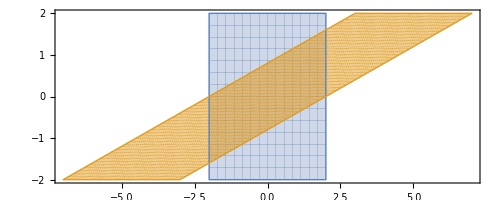

```mathematica
A=({{1, 2.5}, {0, 1}});
ParametricPlot[ {{x1,x2},A.{x1,x2}},{x1,-2,2},{x2,-2,2}]
```

## Dilation

The matrix A=(r | 0
0 | r) is a dilation.  It stretches everything by r.  It has the simple formula
	x→A x = (r | 0
0 | r)x=r x

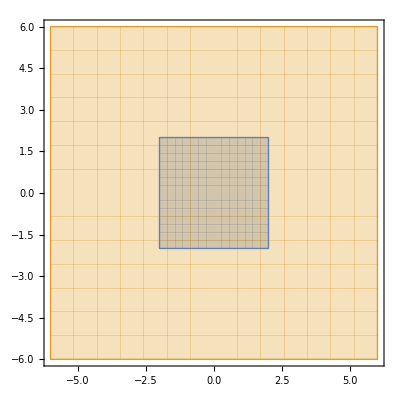

```mathematica
A=({{3, 0}, {0, 3}});
ParametricPlot[ {{x1,x2},A.{x1,x2}},{x1,-2,2},{x2,-2,2}]
```

### Look at Table of pics on p78-80 of text.